```mathematica
FourierTransform[Exp[-x^2],x,ω]
```

(ⅇ^(-ω^2/4))/(√2)

```mathematica
FourierTransform[(Sin[x]/x)^2,x,ω]
```

1/4 √(π/2) (-2 Sign[-2+ω]+ω Sign[-2+ω]-2 ω Sign[ω]+2 Sign[2+ω]+ω Sign[2+ω])

```mathematica
Plot[{FourierTransform[Exp[-x^2],x,ω],FourierTransform[Exp[-0.25x^2],x,ω],FourierTransform[(Sin[x]/x)^2,x,ω],FourierTransform[(Sin[0.5x]/(0.5x))^2,x,ω]},{ω,0,5},PlotStyle->{Red,Green,Directive[Red,Dashed],Directive[Green,Dashed],PlotRange->Automatic}]
```

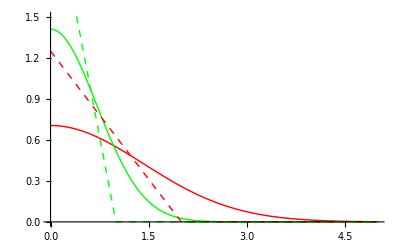

```mathematica
FourierSeries[Exp[-x],x,10]
```

Sinh[π]/π-((1/2+ⅈ/2) ⅇ^(-ⅈ x) Sinh[π])/π-((1/2-ⅈ/2) ⅇ^(ⅈ x) Sinh[π])/π+((1/5+(2 ⅈ)/5) ⅇ^(-2 ⅈ x) Sinh[π])/π+((1/5-(2 ⅈ)/5) ⅇ^(2 ⅈ x) Sinh[π])/π-((1/10+(3 ⅈ)/10) ⅇ^(-3 ⅈ x) Sinh[π])/π-((1/10-(3 ⅈ)/10) ⅇ^(3 ⅈ x) Sinh[π])/π+((1/17+(4 ⅈ)/17) ⅇ^(-4 ⅈ x) Sinh[π])/π+((1/17-(4 ⅈ)/17) ⅇ^(4 ⅈ x) Sinh[π])/π-((1/26+(5 ⅈ)/26) ⅇ^(-5 ⅈ x) Sinh[π])/π-((1/26-(5 ⅈ)/26) ⅇ^(5 ⅈ x) Sinh[π])/π+((1/37+(6 ⅈ)/37) ⅇ^(-6 ⅈ x) Sinh[π])/π+((1/37-(6 ⅈ)/37) ⅇ^(6 ⅈ x) Sinh[π])/π-((1/50+(7 ⅈ)/50) ⅇ^(-7 ⅈ x) Sinh[π])/π-((1/50-(7 ⅈ)/50) ⅇ^(7 ⅈ x) Sinh[π])/π+((1/65+(8 ⅈ)/65) ⅇ^(-8 ⅈ x) Sinh[π])/π+((1/65-(8 ⅈ)/65) ⅇ^(8 ⅈ x) Sinh[π])/π-((1/82+(9 ⅈ)/82) ⅇ^(-9 ⅈ x) Sinh[π])/π-((1/82-(9 ⅈ)/82) ⅇ^(9 ⅈ x) Sinh[π])/π+((1/101+(10 ⅈ)/101) ⅇ^(-10 ⅈ x) Sinh[π])/π+((1/101-(10 ⅈ)/101) ⅇ^(10 ⅈ x) Sinh[π])/π

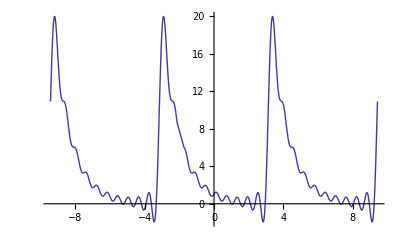

```mathematica
Plot[%,{x,-3Pi,3Pi}]
```

```mathematica
Integrate[Exp[-x-2*Pi*w*x*ⅈ],{x,-5,+5}]
```

```mathematica
Plot[(2 Sinh[5+10 ⅈ π w])/(1+2 ⅈ π w),{w,-5,5}]
```

-Graphics-

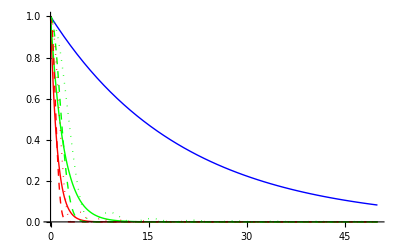

```mathematica
Plot[{Exp[-x],Exp[-0.5*x],Exp[-0.05*x],Exp[-x^2],Exp[-0.25*x^2],(Sin[x]/x)^2,(Sin[0.5x]/(0.5x))^2},{x,0,50},PlotStyle->{Red,Green,Blue,Directive[Red,Dashed],Directive[Green,Dashed],Directive[Red,Dotted],Directive[Green,Dotted]},PlotRange->Full]
```

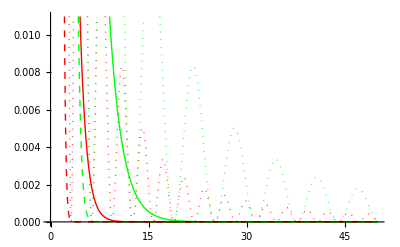

```mathematica
Plot[{Exp[-x],Exp[-0.5*x],Exp[-x^2],Exp[-0.25*x^2],(Sin[x]/x)^2,(Sin[0.5x]/(0.5x))^2},{x,0,50},PlotStyle->{Red,Green,Directive[Red,Dashed],Directive[Green,Dashed],Directive[Red,Dotted],Directive[Green,Dotted]},PlotRange->Automatic]
```